```mathematica
ClearAll[k, n, f];
f[n_, k_]:= k(n-k)((n-1)^2-k^2);
FullSimplify[D[f[n, k], k]]
Collect[D[f[n, k], {k, 2}], k]
```

4 k^3-2 k (-1+n)^2-3 k^2 n+(-1+n)^2 n

12 k^2-2 (-1+n)^2-6 k n

```mathematica
FullSimplify[Solve[4 k^3-2 k (-1+n)^2-3 k^2 n+(-1+n)^2 n==0, k]]
```

{{k→1/36 (9 n+(3 3^(2/3) (8+n (-16+11 n)))/((-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))+3 3^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))},{k→n/4-((-1/3)^(1/3) (8+n (-16+11 n)))/(4 (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))+1/4 (-1/3)^(2/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)},{k→1/72 (18 n+(6 (-3)^(2/3) (8+n (-16+11 n)))/((-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))-6 (-3)^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))}}

```mathematica
Table[n/4+(√(8-16 n+11 n^2))/(4 √3)//N, {n, 1, 10}]
Simplify[-2/3 n+3/2+1/6 √(52 n^2-132n+81)-n/4+(√(8-16 n+11 n^2))/(4 √3)]
```

{0.5,1.1455,1.85868,2.58114,3.30649,4.03311,4.7604,5.48807,6.216,6.9441}

1/12 (18-11 n+√(24-48 n+33 n^2)+2 √(81-132 n+52 n^2))

```mathematica
sols = {{k->1/36 (9 n+(3 3^(2/3) (8+n (-16+11 n)))/(-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)+3 3^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))},{k->n/4-((-1/3)^(1/3) (8+n (-16+11 n)))/(4 (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))+1/4 (-1/3)^(2/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)},{k->1/72 (18 n+(6 (-3)^(2/3) (8+n (-16+11 n)))/(-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)-6 (-3)^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))}};
sols[[1]][[1]][[2]]
```

1/36 (9 n+(3 3^(2/3) (8+n (-16+11 n)))/((-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))+3 3^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))

```mathematica
Table[{N[sols[[3]][[1]][[2]], 100] (*Ideja. zgolj 3-ja rešitev zadošča zgornji meji (vzel sem tisto mejo ki je boljša kot n/2)*)
, -2/3 n+3/2+1/6 Sqrt[52 n^2-132n+81]//N}, {n, 6, 10}]
```

{{2.13679065449300527336629644713108051033517803501922443049239202309057660976161543169359273237423647+0. ⅈ,3.17891},{2.531954118630339983106226804394096727198717289381285797114168561161326107446015348701739045105851222+0. ⅈ,3.71527},{2.925853300312254022141070555011705384858879136625999380551355003018062047117757362361351222538858834+0. ⅈ,4.25129},{3.318929706805445509834616826039865861579890249544525951775477929719426345829370083119808319600982617+0. ⅈ,4.78709},{3.711441339031122288459328513750748509440586249074625593324931071426227642218299462410737598904091642+0. ⅈ,5.32275}}

```mathematica
kk[n_]:= 1/72 (18 n+(6 (-3)^(2/3) (8+n (-16+11 n)))/(-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)-6 (-3)^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3));
zgornjaMeja[n_]:=-2/3 n+3/2+1/6 Sqrt[52 n^2-132n+81];
konveksnaOd[n_]:=n/4+(√(8-16 n+11 n^2))/(4 √3);
konveksnaPred[n_]:= n/4-(√(8-16 n+11 n^2))/(4 √3);
f[n_, k_]:= k(n-k)((n-1)^2-k^2);
Table[{Re[kk[n]//N],zgornjaMeja[n]//N,  konveksnaOd[n]//N}, {n, 5, 10}]

kk[5]//N
```

{{1.73954,2.64191,3.30649},{2.13679,3.17891,4.03311},{2.53195,3.71527,4.7604},{2.92585,4.25129,5.48807},{3.31893,4.78709,6.216},{3.71144,5.32275,6.9441}}

1.73954-3.94746×10^-16 ⅈ

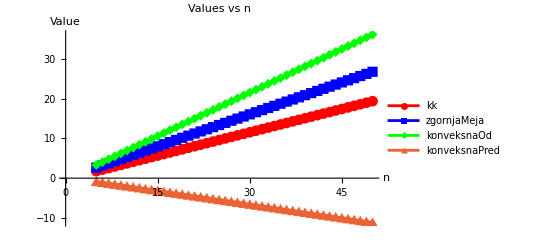

```mathematica
ListLinePlot[Transpose@Table[{Re[kk[n]//N],zgornjaMeja[n]//N,konveksnaOd[n]//N, konveksnaPred[n]},{n,5,50}],DataRange->{5,50},PlotMarkers->Automatic,PlotStyle->{Red,Blue,Green, "purple"},PlotLegends->{"kk","zgornjaMeja","konveksnaOd", "konveksnaPred"},PlotLabel->"Values vs n",AxesLabel->{"n","Value"}]
```

```mathematica
gList[n_]:={Re[kk[n]//N],zgornjaMeja[n]//N,konveksnaOd[n]//N};
colors={Red,Blue,Green};
labels={"kk[n]","zgornjaMeja[n]","konveksnaOd[n]"};

Manipulate[Plot[f[n,k],{k,1,n},PlotRange->All,Epilog->Table[{colors[[i]],Dashed,Line[{{gList[n][[i]],0},{gList[n][[i]],f[n,gList[n][[i]]]}}]},{i,1,3}],AxesLabel->{"k","f(n,k)"},PlotLabel->Dynamic[Row[{"n = ",n}]],PlotLegends->Placed[LineLegend[colors,labels],Right]],{n,5,100,1}  (*integer slider*)] (*Zgleda precej lokalno simetrična okoli vrha, če se bi to dalo dokazat bi se lahko kk: N -> R popravil na N -> N tako da se vzame najbližji integer*)
```

```mathematica
FullSimplify[1/72 (18 n+(6 (-3)^(2/3) (8+n (-16+11 n)))/(-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)-6 (-3)^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)),
Assumptions->n∈Reals]
```

1/72 (18 n+(6 (-3)^(2/3) (8+n (-16+11 n)))/(-9 (-2+n) n (-2+3 n)+4 √(-96+3 n (128+n (-201+2 (73-34 n) n))) Abs[-1+n])^(1/3)-6 (-3)^(1/3) (-9 (-2+n) n (-2+3 n)+4 √(-96+3 n (128+n (-201+2 (73-34 n) n))) Abs[-1+n])^(1/3))

```mathematica
Assuming[n>=5 &&n ∈Integers,ComplexExpand[ReIm[1/72 (18 n+(6 (-3)^(2/3) (8+n (-16+11 n)))/(-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)-6 (-3)^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)) ]]][[1]]
```

n/4-Cos[1/3 Arg[-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n)))))]]/(3^(1/3) ((-9 (-2+n) n (-2+3 n)+4 √3 √((-1+n)^2) ((-32-n (-128+n (201+2 n (-73+34 n))))^2)^(1/4) Cos[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]])^2+48 (-1+n)^2 √((-32-n (-128+n (201+2 n (-73+34 n))))^2) Sin[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]]^2)^(1/6))+(2 n Cos[1/3 Arg[-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n)))))]])/(3^(1/3) ((-9 (-2+n) n (-2+3 n)+4 √3 √((-1+n)^2) ((-32-n (-128+n (201+2 n (-73+34 n))))^2)^(1/4) Cos[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]])^2+48 (-1+n)^2 √((-32-n (-128+n (201+2 n (-73+34 n))))^2) Sin[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]]^2)^(1/6))-(11 n^2 Cos[1/3 Arg[-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n)))))]])/(8 3^(1/3) ((-9 (-2+n) n (-2+3 n)+4 √3 √((-1+n)^2) ((-32-n (-128+n (201+2 n (-73+34 n))))^2)^(1/4) Cos[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]])^2+48 (-1+n)^2 √((-32-n (-128+n (201+2 n (-73+34 n))))^2) Sin[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]]^2)^(1/6))-1/(8 3^(2/3))Cos[1/3 Arg[-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n)))))]] ((-9 (-2+n) n (-2+3 n)+4 √3 √((-1+n)^2) ((-32-n (-128+n (201+2 n (-73+34 n))))^2)^(1/4) Cos[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]])^2+48 (-1+n)^2 √((-32-n (-128+n (201+2 n (-73+34 n))))^2) Sin[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]]^2)^(1/6)+(3^(1/6) Sin[1/3 Arg[-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n)))))]])/((-9 (-2+n) n (-2+3 n)+4 √3 √((-1+n)^2) ((-32-n (-128+n (201+2 n (-73+34 n))))^2)^(1/4) Cos[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]])^2+48 (-1+n)^2 √((-32-n (-128+n (201+2 n (-73+34 n))))^2) Sin[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]]^2)^(1/6)-(2 3^(1/6) n Sin[1/3 Arg[-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n)))))]])/((-9 (-2+n) n (-2+3 n)+4 √3 √((-1+n)^2) ((-32-n (-128+n (201+2 n (-73+34 n))))^2)^(1/4) Cos[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]])^2+48 (-1+n)^2 √((-32-n (-128+n (201+2 n (-73+34 n))))^2) Sin[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]]^2)^(1/6)+(11 3^(1/6) n^2 Sin[1/3 Arg[-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n)))))]])/(8 ((-9 (-2+n) n (-2+3 n)+4 √3 √((-1+n)^2) ((-32-n (-128+n (201+2 n (-73+34 n))))^2)^(1/4) Cos[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]])^2+48 (-1+n)^2 √((-32-n (-128+n (201+2 n (-73+34 n))))^2) Sin[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]]^2)^(1/6))+1/(8 3^(1/6))((-9 (-2+n) n (-2+3 n)+4 √3 √((-1+n)^2) ((-32-n (-128+n (201+2 n (-73+34 n))))^2)^(1/4) Cos[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]])^2+48 (-1+n)^2 √((-32-n (-128+n (201+2 n (-73+34 n))))^2) Sin[1/2 Arg[-32-n (-128+n (201+2 n (-73+34 n)))]]^2)^(1/6) Sin[1/3 Arg[-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n)))))]]

```mathematica
1/72 (18 n+(6 (-3)^(2/3) (8+n (-16+11 n)))/(-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)-6 (-3)^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3))/.{n-> 5}//N

psi = -9 * (n - 2) * n * (3 * n - 2) + 4 * sqrt(3)*sqrt(-(n - 1)**2*(32+n (-128+n (201+2 n (-73+34 n)))))
```

1.73954-3.94746×10^-16 ⅈ

-9 (-2+n) n (-2+3 n)-12 (32+n (-128+n (201+2 n (-73+34 n)))) sqrt^2 (-1+n)**2

```mathematica
Limit[kk[n]/n, {n->Infinity}] (* Limita *)
```

1/12 (3-(ⅈ (-11 3^(2/3)+3^(1/3) (27 ⅈ+8 √51)^(2/3)))/(27 ⅈ+8 √51)^(1/3))

```mathematica
1/12 (3-(ⅈ (-11 3^(2/3)+3^(1/3) (27 ⅈ+8 √51)^(2/3)))/(27 ⅈ+8 √51)^(1/3))//N
```

0.390388+6.93889×10^-17 ⅈ

```mathematica
(√17-1)/8//N
```

0.390388

```mathematica
Limit[Assuming[n>=5 &&n ∈Integers,ComplexExpand[ReIm[1/72 (18 n+(6 (-3)^(2/3) (8+n (-16+11 n)))/(-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)-6 (-3)^(1/3) (-9 (-2+n) n (-2+3 n)+4 √3 √(-(-1+n)^2 (32+n (-128+n (201+2 n (-73+34 n))))))^(1/3)) ]]][[1]]/n, {n->Infinity}]
```

1/12 (3+√33 Cos[1/3 ArcTan[(8 √(17/3))/9]]-3 √11 Sin[1/3 ArcTan[(8 √(17/3))/9]])

```mathematica
FullSimplify[1/12 (3+√33 Cos[1/3 ArcTan[(8 √(17/3))/9]]-3 √11 Sin[1/3 ArcTan[(8 √(17/3))/9]])]
```

1/8 (-1+√17)